# Enumeration of Equivariant Polynomials on Harmonic Tensors

Michael Liu | https://github.com/MichaelLiu2024/Equivariant-Polynomial-Tensor-Functions

## Abstract

We present an algorithm to enumerate a vector space basis for the space of SO(3)-equivariant homogeneous polynomials from harmonic tensors to harmonic tensors. Our approach is to explicitly compute the isotypic decomposition of the symmetric power of a finite dimensional SO(3)-representation using Schur-Weyl duality and Clebsch-Gordan theory.

We use this algorithm to enumerate a module basis for the covariant module over the invariant ring as well as an algebra basis for the invariant ring. Our approach is to extract generators degree by degree using Nakayama’s lemma.

## Preliminaries

#### Definition (Covariant module and invariant ring)

Let G:=SO(3), let X be any finite dimensional G-representation, and let Y be any irreducible G-representation. The covariant module (𝒮(X^*)⊗Y)^G is the space of G-equivariant polynomials from X to Y. The invariant ring (𝒮(X^*))^G is the space of G-invariant polynomials from X to ℂ.

#### Remark

Our first goal is to enumerate a vector space basis for the space (𝒮^D(X^*))^G of homogeneous degree D polynomials in the invariant ring. To do this, we explicitly compute the isotypic decomposition

𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X^*)),

where Λ:=ℕ_0 is the set of irrep labels for G, H_ν is the G-irrep of dimension 2ν+1, and the action of G on the right-hand-side is on the H_ν factor only. Then

(𝒮^D(X^*))^G≅Hom_G(H_0,𝒮^D(X^*)),

which reveals a basis for (𝒮^D(X^*))^G. To parameterize the multiplicity space Hom_G(H_0,𝒮^D(X^*)), we rely on two main tools. The first is the Clebsch-Gordan theory for G=SO(3), which yields an explicit isotypic decomposition of the tensor product of G-irreps.

#### Definition (Elementary Clebsch-Gordan tensor)

For any λ:=(λ_1,λ_2),γ:=(γ_1,γ_2)∈Λ^2 such that λ_1=γ_1 and |λ_1-λ_2|<=γ_2<=λ_1+λ_2, the elementary Clebsch-Gordan tensor CG(λ,γ) is the unique element in (H_λ_1⊗H_λ_2⊗H_γ_2)^G normalized via the Condon–Shortley phase convention.

#### Definition (Iterated Clebsch-Gordan tensor)

For any λ:=(λ_1,…,λ_d),γ:=(γ_1,…,γ_d)∈Λ^d such that λ_1=γ_1 and |λ_j-λ_(j+1)|<=γ_(j+1)<=λ_j+λ_(j+1) for all 1<=j<=d-1, the Clebsch-Gordan tensor CG(λ,γ) is the unique element in (H_λ_1⊗…⊗H_λ_d⊗H_γ_d)^G with the tensor train factorization

CG(λ,γ):=∏_(j=1)^(d-1) CG((γ_j,λ_(j+1)),(γ_j,γ_(j+1))),

where the product denotes tensor contraction.

#### Theorem (Isotypic decomposition of the tensor product of two G-irreps)

Let H_λ_1,H_λ_2 be G-irreps. Then

H_λ_1⊗H_λ_2≅⊕_(γ_2=|λ_1-λ_2|)^(λ_1+λ_2)H_γ_2⊗Hom_G(H_γ_2,H_λ_1⊗H_λ_2).

Moreover, a basis for Hom_G(H_γ_2,H_λ_1⊗H_λ_2) is given by the single Clebsch-Gordan tensor CG(λ,γ), where λ:=(λ_1,λ_2) and γ:=(λ_1,γ_2).

#### Theorem (Isotypic decomposition of the tensor product of multiple G-irreps)

Let H_λ_1,...,H_λ_d be G-irreps. Then

H_λ_1⊗…⊗H_λ_d≅⊕_(μ=Max[0,2m-s])^s H_μ⊗Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d),

where s:=λ_1+…+λ_d and m:=Max[λ_1,…,λ_d]. Moreover, a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d) is given by the Clebsch-Gordan tensors CG(λ,γ), where λ:=(λ_1,…,λ_d), and γ ranges over all γ:=(γ_1,…,γ_d)∈Λ^d such that |λ_j-λ_(j+1)|<=γ_(j+1)<=λ_j+λ_(j+1) and γ_d=μ.

#### Remark

The coordinates of the Clebsch-Gordan tensor in the angular momentum basis are well known. For any λ_1,λ_2,λ_3∈Λ and any m_1,m_2,m_3∈ℤ, denote by

(λ_1 | λ_2 | λ_3
m_1 | m_2 | m_3)∈ℝ

the corresponding Clebsch-Gordan coefficient, which can be computed using the ClebschGordan function in Mathematica. Note that the Clebsch-Gordan coefficient is nonzero iff |λ_1-λ_2|<=λ_3<=λ_1+λ_2, |m_j|<=λ_j for all j, and m_3=m_1+m_2. Then for any valid λ,γ∈Λ^d, we have in coordinates

CG(λ,γ)=∏_(j=1)^(d-1) (γ_j | λ_(j+1) | γ_(j+1)
s_j | m_(j+1) | s_(j+1))∈ℝ^(2 λ_1+1)⊗…⊗ℝ^(2 λ_d+1)⊗ℝ^(2 γ_d+1),

where s_j:=m_1+…+m_j, and the free indices are m_1,…,m_d along with the last index s_d, which is completely determined by the m_j. Note that the Clebsch-Gordan tensor CG(λ,γ) is nonzero iff |γ_j-γ_(j+1)|<=λ_(j+1)<=γ_j+γ_(j+1) for all 1<=j<=d-1 and |m_j|<=λ_j ,|s_j|<=γ_j for all 1<=j<=d. Moreover, it is always the case that (1,2)CG(λ,γ)=(-1)^γ_2 CG(λ,γ).

#### Remark

Schur-Weyl duality is the other tool we use to parameterize the multiplicity space Hom_G(H_0,𝒮^D(X^*)) in the isotypic decomposition of 𝒮^D(X^*). In our context, Schur-Weyl duality provides a clean way to bookkeep any irrep multiplicity in the input space X.

#### Definition (Young symmetrizer)

Let π be an integer partition of d∈ℕ, and let T_π be the associated standard Young tableau filled in English-reading order. Define

R_π:={σ∈𝔖_d|σ preserves every row of T_π},
C_π:={σ∈𝔖_d|σ preserves every column of T_π}.

The row antisymmetrizer, column symmetrizer, and Young symmetrizer are, respectively,

r_π:=1/(|R_π|)∑_(σ∈R_π) sgn(σ)σ,
c_π:=1/(|C_π|)∑_(σ∈C_π) σ,
e_π:=(|R_π||C_π|)/HL_π c_π r_π,

where HL_π is the hook length product of π.

#### Theorem (Schur-Weyl duality)

Let V be a finite dimensional vector space, let the general linear group GL(V) act diagonally on V^(⊗d), and let the symmetric group 𝔖_d act via factor permutation on V^(⊗d). Then

V^(⊗d)≅⊕_π e_π(V^(⊗d))⊗[π]≅⊕_π e_π^*(V^(⊗d))⊗[π]^*,

where the sum is over all integer partitions π of d with largest part at most dim V, and [π] is the Specht module associated with π.

#### Corollary (Cauchy decomposition (Corollary 2.3.3 in [W03]))

Let V,W be finite dimensional. Then

𝒮^d(V⊗W)≅⊕_π e_π(V^(⊗d))⊗e_π^*(W^(⊗d)),

where the sum is over all integer partitions π of d with largest part at most min(dim V,dim W).

#### Lemma (Basis for e_π(V^(⊗d)))

Let V be a vector space with basis {v_1,…,v_n}. Then e_π(V^(⊗d)) has a basis

{e_π(T)|T ranges over all SSYT monomials of shape π filled with entries from {v_1,…,v_n}}.

## Vector Space Basis for the Invariant Ring

### Theory

#### Remark

Given a finite dimensional input space X=⊕_λ H_λ⊗M_λ, our goal in this section is to explicitly bookkeep the isotypic decomposition of its symmetric power 𝒮^D(X).

#### Lemma

There exists a unitary G-equivariant isomorphism

𝒮^D(X)≅⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ^*(M_λ^(⊗d_λ))),

where (d_λ)_λ ranges over all sequences of nonnegative integers such that ∑_λ d_λ=D, and (π_λ)_λ ranges over all sequences of integer partitions such that each π_λ⊢d_λ has largest part at most min(dim H_λ,dim M_λ).

#### Proof

We have

𝒮^D(X)=𝒮^D(⊕_λ H_λ⊗M_λ)
≅^Sym⊕_((d_λ)_λ)⊗_λ 𝒮^d_λ(H_λ⊗M_λ)
≅^(rearrange ⊗, Sym)⊕_((d_λ)_λ)⊗_λ⊕_π_λ e_π_λ(H_λ^(⊗d_λ))⊗e_π_λ^*(M_λ^(⊗d_λ))
≅^(rearrange ⊗)⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ^*(M_λ^(⊗d_λ))),

where the third line is due to the Cauchy decomposition. Since each intermediate isomorphism is unitary and G-equivariant, so is the composition.

#### Lemma

There exists a G-equivariant isomorphism

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅⊕_(ν∈Λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))),

where (μ_λ)_λ ranges over all sequences of nonnegative integers such that each H_μ_λ appears in e_π_λ(H_λ^(⊗d_λ)) and H_ν appears in ⊗_λ H_μ_λ.

#### Proof

We have

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅^(apply Hom)⊗_λ⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))≅^(rearrange ⊗)⊕_((μ_λ)_λ)(⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))).

Clebsch-Gordan yields

⊗_λ H_μ_λ≅^(apply Hom)⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ).

#### Corollary (Isotypic decomposition of 𝒮^D(X))

There exists a G-equivariant isomorphism

𝒮^D(X)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X))≅⊕_(ν∈Λ)⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ^*(M_λ^(⊗d_λ))).

#### Definition (Isotypic data of a polynomial in 𝒮^D(X))

We say that p∈S^D(X) corresponds to the isotypic data in the spaces H_ν, Hom_G(H_ν,⊗_λ H_μ_λ), Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), and e_π_λ^*(M_λ^(⊗d_λ)) if p is the image of this data under the isomorphism in Eq. (1).

#### Remark

By enumerating a basis for the right-hand-side of Eq. (1) and passing this basis through the isomorphism in Eq. (1), we obtain a basis for 𝒮^D(X) that corresponds to the isotypic decomposition of 𝒮^D(X). In particular, we may use the angular momentum basis for H_ν, the Clebsch-Gordan tensor basis for Hom_G(H_ν,⊗_λ H_μ_λ), and the SSYT basis for e_π_λ^*(M_λ^(⊗d_λ)). The only space for which a basis is not currently on hand is Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), so in the following, we describe how to obtain such a basis using Clebsch-Gordan tensor trees.

#### Lemma (Isotypic decomposition of e_π_λ(H_λ^(⊗d_λ)))

Let λ,d_λ,μ_λ∈ℕ_0, and let π_λ=(π_(λ,p))_p be a partition of d_λ. Then

e_π_λ(H_λ^(⊗d_λ))≅⊕_μ_λ H_μ_λ⊗r_π_λ(⊕_((ξ_(λ,p))_p)Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

where (ξ_(λ,p))_p ranges over all sequences of nonnegative integers such that each H_(ξ_(λ,p)) appears in Λ^(π_(λ,p))(H_λ) and H_μ_λ appears in ⊗_p H_(ξ_(λ,p)).

#### Proof

We have

e_π_λ(H_λ^(⊗d_λ))≅r_π_λ(c_π_λ(H_λ^(⊗d_λ)))
≅r_π_λ(⊗_p Λ^(π_(λ,p))(H_λ))
≅^(apply Hom)r_π_λ(⊗_p⊕_(ξ_(λ,p))H_(ξ_(λ,p))⊗Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))
≅^(rearrange ⊗)r_π_λ(⊕_((ξ_(λ,p))_p)(⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

Clebsch-Gordan yields

⊗_p H_(ξ_(λ,p))≅^(apply Hom)⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p))).

Rearrange the tensor product and use the G-equivariance of r_π_λ to conclude.

#### Lemma

Let wt(μ_λ) be the number of SSYT filled from {-λ,...,λ} with total of the boxes μ_λ. The multiplicity of H_μ_λ in the isotypic decomposition of e_π_λ(H_λ^(⊗d_λ)) is wt(μ_λ)-wt(μ_λ+1). In particular, if s_π the Schur polynomial corresponding to π, then wt(μ_λ) is the coefficient of x^μ_λ in s_π(x^-λ,x^(-λ+1),...,x^λ).

#### Theorem (Evaluation scheme)

Let p∈𝒮^D(X^*) be specified via its isotypic data, i.e., a choice of ν, (d_λ)_λ, (π_λ)_λ, (μ_λ)_λ, h_ν∈H_ν, C∈Hom_G(H_ν,⊗_λ H_μ_λ), (L_λ)_λ∈(Hom_G(H_μ_λ,H_λ^(⊗d_λ)))_λ, and SSYT monomials (T_λ)_λ∈(M_λ^(⊗d_λ))_λ. Moreover, write x∈X as

x=⊕_λ x_λ,

where each x_λ∈H_λ⊗M_λ is

x_λ=⊕_k_λ h_(λ k_λ)⊗m_(λ k_λ)

for some h_(λ k_λ)∈H_λ, and some fixed orthonormal basis {m_(λ k_λ)}_(k_λ=1)^(dim M_λ) for M_λ. Then p(x) can be evaluated by contracting the tensor network for p with the SSYT monomial from x,

p(x)=h_ν·C·⊗_λ(r_π L_λ·c_πf(T_λ)),

where f maps m_(λ k_λ) to h_(λ k_λ).

#### Proof

Allowing for arbitrary rearrangements of the tensor product, we have

x^(⊗D)=⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ x_λ^(⊗d_λ))

and

x_λ^(⊗d_λ)=⊕_((k_(λ l))_l)⊗_(l=1)^d_λ h_(λ k_(λ l))⊗⊗_(l=1)^d_λ m_(λ k_(λ l)),

so

x^(⊗D)=⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ⊕_((k_(λ l))_l)⊗_(l=1)^d_λ h_(λ k_(λ l))⊗⊗_(l=1)^d_λ m_(λ k_(λ l))).

Evaluating the pairing 𝒮^D(X^*)𝒮^D(X), we have

p(x)=px^(⊗D)
=(D
(d_λ)_λ)(h_ν·C·⊗_λ L_λ)⊗(⊗_λ e_π_λ^*(T_λ))⊗_λ⊕_((k_(λ l))_l)⊗_l h_(λ k_(λ l))⊗⊗_l m_(λ k_(λ l))
=(D
(d_λ)_λ)(⊕_((k_(λ l))_(λ l))h_ν·C·⊗_λ L_λ⊗_l h_(λ k_(λ l))∏_λ e_π_λ^*(T_λ)⊗_l m_(λ k_(λ l)))
=(h_ν·C·⊗_λ L_λ⊗_l h_(λ k_(λ l)))_((k_(λ l))_(λ l))·(∏_λ e_π_λ^*(T_λ)⊗_l m_(λ k_(λ l)))_((k_(λ l))_(λ l)).

Finally, apply the lemma below to each λ factor -- do this rigorously.

#### Lemma

Let T∈H^(⊗d). Let {S_j}_j be a complete set of semi-standard Young tableaux with shape π⊢d and entries in {1,...,dim M}. Let {U_k}_k be a complete set of Young tableaux with shape π and entries in {1,...,dim M}. Fix any collection h_1,...,h_(dim M)∈H and any ONB m_1,...,m_(dim M)∈M. For any Young tableaux U, let f(U) (resp. g(U)) be the corresponding elementary tensor in H^(⊗d) (resp. M^(⊗d)) whose l^th component is h_(U(l)) (resp. m_(U(l))). Then

∑_k e_π^*(g(S_j))g(U_k)e_π(T)f(U_k)=e_π(T)f(S_j)

where e_π(T)f(U_k) and e_π(T)f(S_j) are viewed as polynomials in the h_1,...,h_(dim M)∈H.

#### Proof

e_π^*(f(S_j))=e_π^*(Φ^(⊗d)g(S_j))=Φ^(⊗d)e_π^*(g(S_j))=Φ^(⊗d)∑_k e_π^*(g(S_j))g(U_k)g(U_k)=∑_k e_π^*(g(S_j))g(U_k)f(U_k),

so

∑_k e_π^*(g(S_j))g(U_k)e_π(T)f(U_k)=e_π(T)e_π^*(f(S_j)).

## Algorithms

#### Remark

Let X=⊕_(λ∈Λ_X)H_λ⊗M_λ for some finite subset Λ_X⊆Λ and finite dimensional multiplicity space M_λ=ℂ^m_λ. Then X can be specified uniquely by the lists (λ)_(λ∈Λ_X) and (m_λ)_(λ∈Λ_X). Moreover, Hom_G(H_ν,𝒮^D(X^*)) can be specified uniquely by (λ)_λ, (m_λ)_λ, ν∈Λ, and D∈ℕ.

#### Remark

#### Remark

To obtain an efficient data structure encoding Eq. (1), one can

turn the sequence of nested direct sums (i.e., the sums over ν, (d_λ)_λ, (π_λ)_λ, and (μ_λ)_λ) into a tree structure, and

at each leaf, enumerate bases for each factor space (i.e., the Hom_G spaces and the e_π_λ^*(M_λ^(⊗d_λ))) in the tensor product.

Thus, our algorithm splits into two stages.

#### Algorithm (IsotypicDataTree)

Inputs: (λ∈Λ)_λ, (m_λ∈ℕ)_λ, ν∈Λ, D_max∈ℕ
Require: Length[(λ)_λ]=Length[(m_λ)_λ], ∑_λ m_λ<=D_max
Output: IsotypicDataTree

store {λs,mλs,ν} at the root of a tree

for each D∈{∑_λ m_λ,...,D_max}

spawn a new leaf containing D

for each leaf D

for each (d_λ∈ℕ)_λ with ∑_λ d_λ=D

spawn a new leaf containing (d_λ)_λ

for each leaf (d_λ)_λ

for each (π_λ⊢d_λ)_λ with each π_(λ,1)<=min{dim H_λ,dim M_λ}

spawn a new leaf containing (π_λ)_λ

for each leaf (π_λ)_λ

for each (μ_λ∈Λ)_λ with each H_μ_λ appearing in e_π_λ(H_λ^(⊗d_λ)) and H_ν appearing in ⊗_λ H_μ_λ

spawn a new leaf containing (μ_λ)_λ

#### Algorithm (Enumeration of isotypic components in e_π_λ(H_λ^(⊗d_λ)))

Inputs:

λ∈Λ

integer partition π_λ

Algorithm:

#### Algorithm (Enumeration of tensor product bases in Eq. (1))

for each path from root to leaf

compute a basis for Hom_G(H_ν,⊗_λ H_μ_λ)

compute a basis for each Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))

enumerate all SSYT with shapes (π_λ)_λ filled with entries from {1,...,dim M_λ}

#### Pass from isotypic data to polynomials

for each path from root to leaf

take Tuples and contract to compute a tensor basis for Hom_G(H_ν,⊗_λ e_π_λ(H_λ^(⊗d_λ)))

use the evaluation scheme

#### Basis for Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))

explain random sampling approach in ClebschGordanPathsSchurPower

## Algebra Basis for the Invariant Ring

### Theory

Write R=(𝒮(X^*))^G for the invariant ring. Write N=R=(𝒮(X^*))^G or N=(𝒮(X^*)⊗Y)^G for the invariant ring or covariant module, which we view as a modules over R.

#### Lemma (Nakayama)

Let N=⊕_(D∈ℕ_0)N_D be a finitely generated graded module over a graded ring R=⊕_(D∈ℕ_0)R_D, where R_0=ℝ. Let I:=⊕_(D∈ℕ)R_D be the ideal generated by the positively graded elements of R. Let L⊆N. Then L/I N is a basis for N/I N as an ℝ-vector space iff L is a minimal generating set for N as an R-module.

#### Theorem

Suppose that we are given vector space bases ℛ_D,𝒩_D for R_D,N_D. Note that

I N=⊕_(D∈ℕ)(I N)_D,

where

(I N)_D:=I N∩N_D=∑_(1<=D'<=D) R_D' N_(D-D')=Span{r_D' m_(D-D')|1<=D'<=D,r_D'∈ℛ_D',m_(D-D')∈𝒩_(D-D')}.

Since

N/I N≅⊕_(D∈ℕ)N_D/(I N)_D,

we can proceed degree-by-degree to obtain a vector space basis for N/I N. Define

D_max:=max{D∈ℕ|N_D/(I N)_D!=0},

which may be difficult to determine in practice.

For each 1<=D<=D_max, compute a basis for (I N)_D and extend it to a basis for N_D by adjoining the basis vectors in the set L_D⊆N_D. Write L:=∪_(D∈ℕ)L_D. Since L_D/(I N)_D is a basis for N_D/(I N)_D, L/I N is a basis for N/I N, so by Nakayama’s Lemma, L is a minimal generating set for N as an R-module.

Next, apply the above algorithm with N=I. Let ℝ[L] be the ℝ-algebra generated by L. Clearly, ℝ⊆ℝ[L]. Now, write R_(<=D):=R_0⊕…⊕R_D, and suppose that R_(<=D)⊆ℝ[L]. Then

R_(D+1)=I_(D+1)⊆Span_ℝ(L_(D+1))+(I^2)_(D+1)=Span_ℝ(L_(D+1))+∑_(1<=D'<=D) I_D' I_(D+1-D').

Clearly, Span_ℝ(L_(D+1))⊆ℝ[L], and by the inductive hypothesis, I_1,...,I_D⊆R_(<=D)⊆ℝ[L]. Thus, R=ℝ[L]. To see that L is minimal, note that if any L⊆I generates R as an ℝ-algebra, then L generates I as an R-module, so L/I^2 generates I/I^2 as an ℝ-module. Thus, since our given L makes L/I^2 a basis for I/I^2, our given L is a minimal generating set for R as an ℝ-algebra.

### Algorithms

Given D_max∈ℕ and ℛ_D,𝒩_D for all D=0,1,2,...,D_max,

For D=1,2,...,D_max

compute a basis for (I N)_D

extend the above to a basis for N_D by evaluating the new basis vectors in 𝒩_D at the same random points and finding pivot columns L_D

#### Compute a basis for (I N)_D

For D'=1,2,...,D

For r_D'∈ℛ_D',m_(D-D')∈𝒩_(D-D')

evaluate r_D' and m_(D-D') at random points and Outer

#### Comments

In practice, we can cut out obvious algebraic independence from 𝒩_D, but not necessarily from 𝒩_(D-D').

Let’s send the vector space dimensions/minimal generating set sizes through OEIS and see if anything comes up? We can see if the Hilbert series are already known somewhere and try to make connections here

## Vector Space Basis for the Covariant Module

### Theory

#### Corollary (Isotypic decomposition of the covariant module)

Let Y=H_ρ. The isotypic decomposition of the D^th graded piece of the covariant module is

(𝒮^D(X^*)⊗Y)^G≅(H_ρ⊗H_ρ)^G⊗Hom_G(H_ρ,𝒮^D(X^*)).

In particular, a basis for the covariant module can be obtained as follows. First, apply the Clebsch-Gordan map embedding H_0->(H_ρ⊗H_ρ)^G to obtain the unique G-invariant vector v in H_ρ⊗H_ρ. Then, for each basis vector m in Hom_G(H_ρ,𝒮^D(X^*)) specified by its isotypic data, send v⊗m through the isomorphism in Eq. (1) to obtain the corresponding basis vector in (𝒮^D(X^*)⊗Y)^G.

#### Conjecture

If a degree d invariant spin tree has a 0 interior node, then that tree is a product of lower degree invariants. Hence, when looking for algebra/module generators, we can discard any tree with any 0 interior node

#### Proof

Suppose there is a 0 interior node. The leaves of its subtree combine to 0. The leaves in the complement combine to the root. They are multiplied. So this means the 0 subtree is an invariant coefficient of the invariant/covariant in the complement subtree.

#### Conjecture

Can the SSYT be ignored? Can the Young symmetrizer be ignored? Can inputs be plugged into the unsymmetrized tensor trees?

#### Conjecture

If there are multiple SSYT, then the tensor tree is not algebraically independent. If this conjecture holds, then maybe we can replace the SSYT with just feeding the default SSYT (variable j fills the j^th column), which corresponds to the usual evaluation at the variables. Maybe the only SSYT is the default SSYT?

### Algorithms

#### Overview

Run previous algorithm to obtain maps

Single CG step

Combine maps

## Appendix A: Lemmas

#### Lemma A1 (Identifying the covariant module with the space of equivariant polynomial functions)

There is an isomorphism of vector spaces

(𝒮(X^*)⊗Y)^G≅{equivariant polynomial functions from X to Y}

#### Proof

Consider the pairing (𝒮(X^*)⊗Y)×X->Y defined on elementary tensors (which correspond to the component functions of the polynomial) by

(φ⊗y,x)↦(φ⊗y)(x):=φ(x)y

and extended linearly to 𝒮(X^*)⊗Y, where φ(x) is defined by writing

φ=⊕_(d=0)^D⊕_(j_1,…,j_d=1)^(dim X^*)φ_(j_1(…j)_d)e_j_1^*⊗…⊗e_j_d^*

in terms of a basis {e_j^*}_(j=1)^(dim X^*) for X^* and declaring that

φ(x):=⊕_(d=0)^D⊕_(j_1,…,j_d=1)^(dim X^*)φ_(j_1(…j)_d)e_j_1^*(x)*…*e_j_d^*(x).

Note that φ(x) is a degree D polynomial in the entries of X selected by the e_j^*.

Fix g∈G, ∑_i φ_i⊗y_i∈𝒮(X^*)⊗Y, and x∈X. Observe that

(∑_i φ_i⊗y_i)(g x)=g((∑_i φ_i⊗y_i)(x))
⟺∑_i φ_i(g x)y_i=g(∑_i φ_i(x)y_i)
⟺∑_i (g^-1 φ_i)(x)y_i=∑_i φ_i(x)g y_i
⟺(∑_i g^-1 φ_i⊗y_i)(x)=(∑_i φ_i⊗g y_i)(x).

Thus, we conclude that the polynomial ∑_i φ_i⊗y_i is equivariant iff g∑_i φ_i⊗y_i=∑_i φ_i⊗y_i for all g∈G iff ∑_i φ_i⊗y_i∈(𝒮(X^*)⊗Y)^G.

#### Lemma A3 (Angular momentum basis for H_λ)

Let

1,1:=1/(√2)(-1
-ⅈ
0)

and

J_-:=1/(√2)(0 | 0 | 1
0 | 0 | -ⅈ
-1 | ⅈ | 0).

For any nonzero λ∈Λ and any integer -λ<=m<=λ, write

𝒥_-:=∑_(l=0)^(λ-1) 𝟙^(⊗l)⊗J_-⊗𝟙^(⊗λ-1-l),

and define

λ,m:=√(((λ+m)!)/((2λ)!(λ-m)!))𝒥_-^(λ-m)(1,1)^(⊗λ).

Then {λ,m}_(-λ<=m<=λ) is an orthonormal basis for H_λ.

#### Lemma (Computing a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d))

Let λ_1,…,λ_d∈Λ. Let ℐ be the Listable Folded function ℐ[a,b]:=Range[Abs[a-b],a+b]. For any index α into ℐ(λ_1,…,λ_d), define γ_1(α):=λ_1 and

γ_j(α):=|γ_(j-1)(α)-λ_j|+α_(j-1)-1

for all 2<=j<=d. Then a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d) is given by the Clebsch-Gordan tensors CG(λ,γ(α)), where α ranges over all indices into ℐ(λ_1,…,λ_d) that land at μ.

#### Lemma (Isotypic decomposition of Λ^d(H_λ))

Suppose that λ,d<=3. Then

dim Hom_G(H_μ,Λ^d(H_λ))<=1.

Moreover, prove that for d=3 and all μ, {λ,#+1-Mod[#,2]&@Abs[λ-μ],μ} is a nonzero path. Worst case, we can verify this computationally. We might be able to just prove this for all λ by staring at the explicit form of the CG tensor.

#### Proof

We check the isotypic multiplicities by brute force.

```mathematica
data=Table[IsotypicMultiplicityExteriorPower[λ,d,μ],{λ,0,3},{d,1,2λ+1},{μ,0,Sum[i,{i,λ-d+1,λ}]}];
Grid[data,ItemSize->Full]
```

{1} |  |  |  |  |  | 
{0,1} | {0,1} | {1} |  |  |  | 
{0,0,1} | {0,1,0,1} | {0,1,0,1} | {0,0,1} | {1} |  | 
{0,0,0,1} | {0,1,0,1,0,1} | {1,0,1,1,1,0,1} | {1,0,1,1,1,0,1} | {0,1,0,1,0,1} | {0,0,0,1} | {1}

#### Lemma

1/2(id+(1,2))1/3(id-(1,3)-(2,3))=1/6∑_(σ∈𝔖_3) sgn(σ)σ. In particular, can use this in the evaluation scheme for Clebsch-Gordan tensors that are automatically Antisymmetric[{1,2}].

#### Lemma (Polarization identity for symmetric tensors) https://math.stackexchange.com/questions/481167/polarization-formula

There is a bijection

𝒮^d(V)≅{homogeneous degree d polynomials}

which is given explicitly by

ϕ(v):=Φv^(⊗d),
Φv_1⊗…⊗v_d:=(-1)^d/(d!)∑_(A⊆{1,…,d}) (-1)^(|A|)ϕ(∑_(a∈A) v_a).

#### Corollary (Polarization identity for block-symmetric tensors in three variables)

There is a bijection

𝒮^c_1(V)⊗𝒮^c_2(V)⊗𝒮^c_3(V)≅{block homogeneous multidegree (c_1,c_2,c_3) polynomials in three variables}

which is given explicitly by

ϕ(x,y,z):=Φx^(⊗c_1)⊗y^(⊗c_2)⊗z^(⊗c_3),
Φx_1⊗…⊗x_c_1⊗y_1⊗…⊗y_c_2⊗z_1⊗…⊗z_c_3:=(-1)^c_1/(c_1!)(-1)^c_2/(c_2!)(-1)^c_3/(c_3!)∑_(A_1⊆{1,…,c_1}) ∑_(A_2⊆{1,…,c_2}) ∑_(A_3⊆{1,…,c_3}) (-1)^(|A_1|)(-1)^(|A_2|)(-1)^(|A_3|)ϕ(∑_(a_1∈A_1) x_a_1,∑_(a_2∈A_2) y_a_2,∑_(a_3∈A_3) z_a_3).

## Appendix B: Examples

```mathematica
Quit
```

### Load Packages

```mathematica
AppendTo[$Path,"C:\\Users\\micha\\OneDrive\\Desktop\\Oden\\Notes\\Equivariant-Polynomial-Tensor-Functions-main\\Equivariant-Polynomial-Tensor-Functions-main"];
```

```mathematica
Needs["GrowMultiplicitySpaceTree`"];
Needs["UnitTestTools`"]
```

```mathematica
SpinListToSpinTree[{λs_List,γs_List}]:=
If[
Depth[λs]>2,
SpinListToSpinTree[{SpinListToSpinTree/@λs,γs}],
Fold[Tree[Last@#2,{#1,First@#2}]&,First[λs],Rest@Transpose[{λs,γs}]]
]
SpinListToSpinTree[γs_List]:=With[{λ=First@γs},If[Length[γs]==1,Tree[λ,{λ}],Fold[Tree[#2,{#1,λ}]&,γs]]]
```

```mathematica
DisplaySpinTrees[assoc_Association]:={assoc,Outer[SpinListToSpinTree@*List,Tuples[assoc[["leafPaths"]]],assoc[["corePaths"]],1]}
```

### Examples

#### Example (Scalar invariants of one matrix and one vector: X=H_1⊗ℂ^1⊕H_2⊗ℂ^1, Y=H_0, D<=3)

```mathematica
λs={1,2};
mλs={1,1};
ν=0;
dMax=4;
polys=EnumerateVectorSpaceBases[λs,mλs,ν,dMax];
```

```mathematica
v1=SymmetricTensor[1,1];
a1=SymmetricTensor[2,1];
FullSimplify[
1/polys*
{
{v1.v1,Tr[a1.a1]},

{v1.a1.v1,Tr[a1.a1.a1]},

{v1.v1 v1.v1,v1.v1 Tr[a1.a1],v1.a1.a1.v1-1/3 v1.v1 Tr[a1.a1],Tr[a1.a1.a1.a1]}
},
Assumptions->_∈Reals∧Tr[a1]==0
]
```

{{-√3,(2 √5)/3},{√(10/3),-(√70)/9},{3,-2 √(5/3),-(√(35/3))/3,10/9}}

#### Example (Scalar invariants of one vector: X=H_1⊗ℂ^1, Y=H_0, D<=8)

We first compute the isotypic decomposition of the symmetric power as in Eq. (1),

𝒮^D(X)≅⊕_(ν∈Λ)⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ^*(M_λ^(⊗d_λ))).

To do this, we enumerate the nested direct sums, which are naturally organized into a tree structure, and the tensor products, which are most efficiently represented by enumerating a basis for each factor space. We do this for all symmetric powers with degrees 1<=D<=8.

```mathematica
λs={1};(*list of irreps that appear in X*)
mλs={1};(*list of multiplicities of the irreps that appear in X*)
ν=0;(*irrep label for Y=Subscript[H, ν]*)
dMax=4;(*maximum polynomial degree*)
tree=EnumerateVectorSpaceBases[λs,mλs,ν,dMax]
```

{{-((x[{1}][1])^2+(x[{2}][1])^2+(x[{3}][1])^2)/(√3),1/3 ((x[{1}][1])^2+(x[{2}][1])^2+(x[{3}][1])^2)^2}}

The levels of the isotypic data tree can be interpreted as follows.

Level | Symbol | Meaning
0(root) | {(λ)_λ,(dim M_λ)_λ,ν} | concise encoding of the input and output spaces X=⊕_λ H_λ⊗M_λ and Y=H_ν
1 | D | total degree of the polynomial in 𝒮^D(X)
2 | (d_λ)_λ | multidegree in the H_λ:total number of vector/matrix/3–tensor/… terms in the polynomial irrespective of multiplicity
3 | (π_λ)_λ | partitions determining the partial symmetry of tensors
4 | (μ_λ)_λ | the intermediate spins that are directly coupled to H_ν
5(leaves) | - | bases forHom_G(H_ν,⊗_λ H_μ_λ),the Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))),and the e_π_λ^*(M_λ^(⊗d_λ))

Using this tree, we see that Eq. (1) simplifies to

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^1)≅Hom_G(H_0,𝒮^2(H_1)).

Next, for each tuple of isotypic data, we contract the corresponding (Young symmetrized) tensor tree with the chosen SSYT monomial in the input tensors to obtain an equivariant polynomial. This produces a basis for Hom_G(H_ν,𝒮^D(X)). In this example, the spin trees are

```mathematica
polys=TreeData/@TreeLeaves[tree];
```

In the above, the first subscript represents the multiplicity index (which tensor this coordinate is coming from), and the second subscript represents the Cartesian coordinate. We check that this is (‖·‖)^2 up to some scalar multiple,

```mathematica
v=SymmetricTensor[1,1];
FullSimplify[{v.v,v.v v.v,v.v v.v v.v,v.v v.v v.v v.v}/polys,Assumptions->_∈Reals]
```

{{-√3},{3},{-3 √3},{9}}

#### Example (Scalar invariants of two vectors: X=H_1⊗ℂ^2, Y=H_0, D<=8)

As in the previous example, we first simplify Eq. (1) by forming the isotypic data tree.

```mathematica
λs={1};
mλs={2};
ν=0;
dMax=4;
tree=EnumerateVectorSpaceBases[λs,mλs,ν,dMax]
```

{{-((x[{1}][1])^2+(x[{2}][1])^2+(x[{3}][1])^2)/(√3),-(x[{1}][1] x[{1}][2]+x[{2}][1] x[{2}][2]+x[{3}][1] x[{3}][2])/(√3),1/(2 √3)((x[{1}][2])^2 ((x[{2}][1])^2+(x[{3}][1])^2)+(x[{2}][2] x[{3}][1]-x[{2}][1] x[{3}][2])^2-2 x[{1}][1] x[{1}][2] (x[{2}][1] x[{2}][2]+x[{3}][1] x[{3}][2])+(x[{1}][1])^2 ((x[{2}][2])^2+(x[{3}][2])^2)),1/3 ((x[{1}][1])^2+(x[{2}][1])^2+(x[{3}][1])^2)^2,1/3 ((x[{1}][1])^2+(x[{2}][1])^2+(x[{3}][1])^2) (x[{1}][1] x[{1}][2]+x[{2}][1] x[{2}][2]+x[{3}][1] x[{3}][2]),1/9 ((x[{1}][2])^2 ((x[{2}][1])^2+(x[{3}][1])^2)+(x[{2}][2])^2 (3 (x[{2}][1])^2+(x[{3}][1])^2)+4 x[{2}][1] x[{2}][2] x[{3}][1] x[{3}][2]+((x[{2}][1])^2+3 (x[{3}][1])^2) (x[{3}][2])^2+4 x[{1}][1] x[{1}][2] (x[{2}][1] x[{2}][2]+x[{3}][1] x[{3}][2])+(x[{1}][1])^2 (3 (x[{1}][2])^2+(x[{2}][2])^2+(x[{3}][2])^2))}}

This tells us that

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^2)≅Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^2),
(𝒮^4(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗(Hom_G(H_0,e_{2,2}(H_1^(⊗4)))⊗e_{2,2}((ℂ^2)^(⊗4))⊕Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^2))≅Hom_G(H_0,e_{2,2}(H_1^(⊗4)))⊗e_{2,2}((ℂ^2)^(⊗4))⊕Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^2).

and we compute the equivariant polynomials

```mathematica
polys=TreeData/@TreeLeaves[tree];
```

These turn out to be the following scalar invariants

```mathematica
v1=SymmetricTensor[1,1];
v2=SymmetricTensor[1,2];
FullSimplify[
1/polys
{
v1.v1,v1.v2,
(v1×v2).(v1×v2),
v1.v1 v1.v1,
v1.v1 v1.v2,
v1.v1 v2.v2+2v1.v2 v1.v2
},
Assumptions->_∈Reals
]
```

{{-√3},{-√3},{2 √3},{3},{3},{9}}

#### Example (Scalar invariants of three vectors: X=H_1⊗ℂ^3, Y=H_0, D<=8)

This example reveals the fully antisymmetric Levi-Civita tensor ϵ when three distinct vectors become available as inputs. In the previous examples, not enough vectors were available for ϵ to appear.

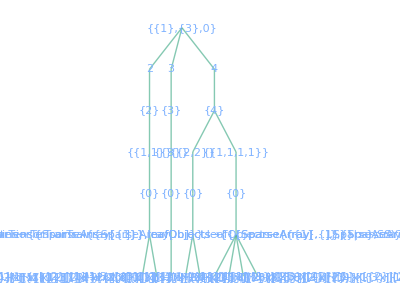

```mathematica
λs={1};
mλs={3};
ν=0;
dMax=4;
tree=IsotypicDataTree[λs,mλs,ν,dMax]
```

The isotypic decompositions of the symmetric powers in this example are

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^3)≅Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^3),
(𝒮^3(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,Λ^3(H_1))⊗Λ^3(ℂ^3)≅Hom_G(H_0,Λ^3(H_1))⊗Λ^3(ℂ^3),
(𝒮^4(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^1)≅Hom_G(H_0,𝒮^4(H_1)).

and the equivariant polynomials are

```mathematica
polys=TreeData/@TreeLeaves[tree];
```

These correspond to the scalar invariants below

```mathematica
v1=SymmetricTensor[1,1];
v2=SymmetricTensor[1,2];
v3=SymmetricTensor[1,3];
FullSimplify[
1/polys
{
v1.v1,
v1.v2,
(v1×v2).v3,
(v1×v2).(v1×v2),
(v1×v2).(v1×v3),
v1.v1 v1.v1,
v1.v1 v1.v2,
v1.v1 v2.v2+2v1.v2 v1.v2,
v1.v1 v2.v3+2v1.v2 v1.v3
},
Assumptions->_∈Reals
]
```

{{-√3},{-√3},{ⅈ √6},{2 √3},{2 √3},{3},{3},{9},{9}}

#### Example (Scalar invariants of one matrix: X=H_2⊗ℂ^1, Y=H_0, D<=3)

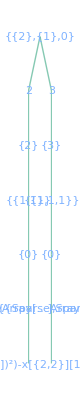

```mathematica
λs={2};
mλs={1};
ν=0;
dMax=3;
tree=IsotypicDataTree[λs,mλs,ν,dMax]
```

Eq. (1) simplifies to

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_2))⊗𝒮^2(ℂ^1)≅Hom_G(H_0,𝒮^2(H_2)),
(𝒮^3(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^3(H_2))⊗𝒮^3(ℂ^1)≅Hom_G(H_0,𝒮^3(H_2)),

which could have been observed directly.

```mathematica
polys=TreeData/@TreeLeaves[tree];
```

```mathematica
a=SymmetricTensor[2,1];
FullSimplify[{Tr@MatrixPower[a,2],Tr@MatrixPower[a,3]}/polys,Assumptions->_∈Reals∧Tr[a]==0]
```

{{(2 √5)/3},{-(√70)/9}}

#### Example (Scalar invariants of two matrices: X=H_2⊗ℂ^2, Y=H_0, D<=3)

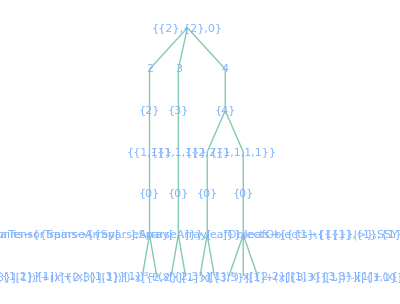

```mathematica
λs={2};
mλs={2};
ν=0;
dMax=4;
tree=IsotypicDataTree[λs,mλs,ν,dMax]
```

```mathematica
polys=TreeData/@TreeLeaves[tree];
```

```mathematica
a1=SymmetricTensor[2,1];
a2=SymmetricTensor[2,2];
ϵ=LeviCivitaTensor[3];
FullSimplify[
1/polys
{
Tr[a1.a2],
Tr[a1.a1.a2],
Tr[a1.a2.ϵ.ϵ.a2.a1],Flatten[a1.ϵ.a2].Flatten[a1.ϵ.a2]+Flatten[a1.ϵ.a2].Flatten[a2.ϵ.a1],t,t,t,t,t
},
Assumptions->_∈Reals∧Tr[a1]==0∧Tr[a2]==0
]
```

#### Example (Scalar invariants of one 3-tensor: X=H_3⊗ℂ^1, Y=H_0, D<=3)

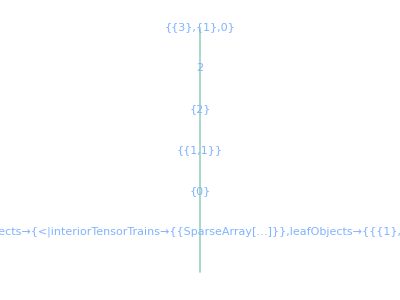

```mathematica
λs={3};
mλs={1};
ν=0;
dMax=3;
tree=IsotypicDataTree[λs,mλs,ν,dMax]
```

```mathematica
polys=TreeData/@TreeLeaves[tree];
```

```mathematica
a1=SymmetricTensor[3,1];
FullSimplify[{(Norm[Flatten@a1,2])^2}/polys,Assumptions->_∈Reals∧Tr[a1]==0]
```

{{-((√7 ((x[{1,1,1}][1])^2+3 (x[{1,1,2}][1])^2+3 (x[{1,1,3}][1])^2+3 (x[{1,2,2}][1])^2+6 (x[{1,2,3}][1])^2+3 (x[{1,3,3}][1])^2+(x[{2,2,2}][1])^2+3 ((x[{2,2,3}][1])^2+(x[{2,3,3}][1])^2)+(x[{3,3,3}][1])^2))/((x[{1,1,1}][1])^2+6 (x[{1,1,2}][1])^2+6 (x[{1,1,3}][1])^2+6 (x[{1,2,2}][1])^2+15 (x[{1,2,3}][1])^2-3 x[{1,2,2}][1] x[{1,3,3}][1]+6 (x[{1,3,3}][1])^2-3 x[{1,1,1}][1] (x[{1,2,2}][1]+x[{1,3,3}][1])+(x[{2,2,2}][1])^2-3 x[{1,1,3}][1] x[{2,2,3}][1]+6 (x[{2,2,3}][1])^2-3 x[{2,2,2}][1] x[{2,3,3}][1]+6 (x[{2,3,3}][1])^2-3 x[{1,1,2}][1] (x[{2,2,2}][1]+x[{2,3,3}][1])-3 (x[{1,1,3}][1]+x[{2,2,3}][1]) x[{3,3,3}][1]+(x[{3,3,3}][1])^2))}}

#### Example (Scalar invariants of two matrices and one 3-tensor: X=H_2⊗ℂ^2⊕H_3⊗ℂ^1, Y=H_0, D<=3)

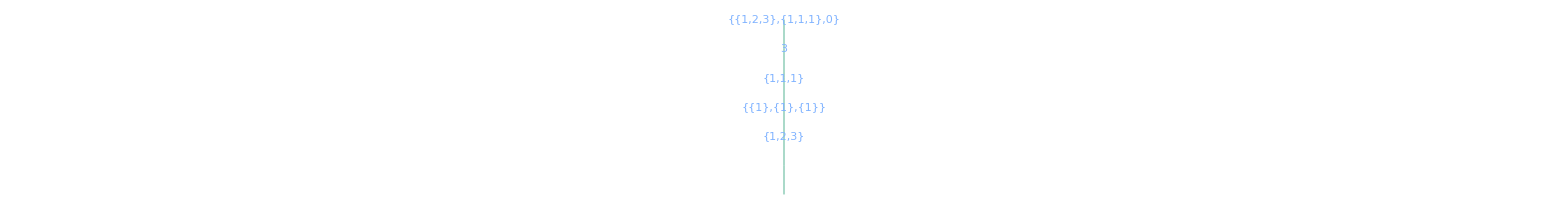

```mathematica
λs={1,2,3};
mλs={1,1,1};
ν=0;
dMax=3;
tree=IsotypicDataTree[λs,mλs,ν,dMax]
```

```mathematica
polys=TreeData/@TreeLeaves[tree]
```

{{1/2 √(3/35) (x[{2}][1] (-10 x[{1,3}][1] x[{1,2,3}][1]+2 x[{1,2}][1] (x[{1,1,1}][1]-4 x[{1,2,2}][1]+x[{1,3,3}][1])+x[{3,3}][1] (x[{1,1,2}][1]+x[{2,2,2}][1]-4 x[{2,3,3}][1])+x[{1,1}][1] (-4 x[{1,1,2}][1]+x[{2,2,2}][1]+x[{2,3,3}][1])+x[{2,2}][1] (3 x[{1,1,2}][1]-2 x[{2,2,2}][1]+3 x[{2,3,3}][1])+2 x[{2,3}][1] (x[{1,1,3}][1]-4 x[{2,2,3}][1]+x[{3,3,3}][1]))+x[{3}][1] (-10 x[{1,2}][1] x[{1,2,3}][1]+2 x[{1,3}][1] (x[{1,1,1}][1]+x[{1,2,2}][1]-4 x[{1,3,3}][1])+2 x[{2,3}][1] (x[{1,1,2}][1]+x[{2,2,2}][1]-4 x[{2,3,3}][1])+x[{3,3}][1] (3 (x[{1,1,3}][1]+x[{2,2,3}][1])-2 x[{3,3,3}][1])+x[{2,2}][1] (x[{1,1,3}][1]-4 x[{2,2,3}][1]+x[{3,3,3}][1])+x[{1,1}][1] (-4 x[{1,1,3}][1]+x[{2,2,3}][1]+x[{3,3,3}][1]))+x[{1}][1] (x[{3,3}][1] (x[{1,1,1}][1]+x[{1,2,2}][1]-4 x[{1,3,3}][1])+x[{2,2}][1] (x[{1,1,1}][1]-4 x[{1,2,2}][1]+x[{1,3,3}][1])+x[{1,1}][1] (-2 x[{1,1,1}][1]+3 (x[{1,2,2}][1]+x[{1,3,3}][1]))+2 (-5 x[{2,3}][1] x[{1,2,3}][1]+x[{1,2}][1] (-4 x[{1,1,2}][1]+x[{2,2,2}][1]+x[{2,3,3}][1])+x[{1,3}][1] (-4 x[{1,1,3}][1]+x[{2,2,3}][1]+x[{3,3,3}][1]))))}}

## References

[W03]	https://doi.org/10.1017/CBO9780511546556

## Old Stuff

Vector space bases for (𝒯^m(V))^(O(V)) and (𝒯^m(V))^(SO(V)) are known explicitly.

#### Old Code

```mathematica
NonzeroQ[array_?ArrayQ]:=Total[Abs@Chop@N@array,∞]!=0
```

```mathematica
computeTable[λ_,p_,μ_]:=
Module[
{paths,tensors},

paths=ClebschGordanPathsSchurPower[λ,p,μ];
tensors=TensorBasisSchurPower[λ,p,μ];

{{{IsotypicMultiplicitySchurPower[λ,p,μ]}},Flatten[Last@paths,1],{Map[NonzeroQ,tensors]}}
]
```

```mathematica
plotTable[{πs_,βs_,table_}]:=
Module[
{rowTicks,colnTicks},

rowTicks=Transpose[{Range[Length[πs]],πs}];
colnTicks=Transpose[{Range[Length[βs]],MatrixForm/@βs}];

ArrayPlot[table,FrameTicks->{rowTicks,Range[Length[βs]],Range[Length[πs]],colnTicks},Mesh->True,Frame->True,ImageSize->1->32]
]
```

#### Scratch

Definition:  The tensor algebra on V is the graded ℝ-algebra

𝒯(V):=⊕_(d∈ℕ_0)𝒯^d(V),
𝒯^d(V):=V^(⊗d).

The symmetrization map on 𝒯(V) is the linear map

Sym:𝒯(V)->𝒯(V),
v_1⊗…⊗v_d↦1/(d!)∑_(σ∈Σ_d) v_(σ(1))⊗…⊗v_(σ(d)).

The symmetric algebra on V is the commutative graded ℝ-algebra

𝒮(V):=Sym(𝒯(V))=⊕_(d∈ℕ_0)𝒮^d(V),
𝒮^d(V):=Sym(𝒯^d(V)),

with multiplication given by the shuffle product

⊙:𝒮(V)×𝒮(V)->𝒮(V),
(a,b)↦a⊙b:=Sym(a⊗b).

Lemma: Let G act linearly on vector spaces V,{V_α}_α. Then

g∈G acts on φ∈V^* by g φ:=φ∘g^-1,

g∈G acts on ⊕_α v_α∈⊕_α V_α by g⊕_α v_α:=⊕_α g v_α, and

g∈G acts on ⊗_α v_α∈⊗_α V_α by g⊗_α v_α:=⊗_α g v_α provided that the tensor product over α is finite.

Moreover, with respect to the above actions, there exist equivariant isomorphisms (which necessarily have equivariant inverses)

(⊕_α V_α)⊗V≅⊕_α(V_α⊗V) and

(⊕_α V_α)^*≅⊕_α V_α^* provided that the sum over α is finite.

Lemma: Let V,M be representations of G.

If M is fixed by G, then (V⊗M)^G=V^G⊗M.

Hom(V,M)≅(V^*⊗M)^G.

Lemma (Schur): Let V,W be irreducible representations of G, and let φ∈Hom(V,W). Then φ=0 or φ is an isomorphism. In particular, either Hom(V,W)=0 or Hom(V,W)≅ℂ.

Proposition: R is a graded subalgebra of 𝒮(X^*). If conditions, then M is a finitely generated graded R-module.

Proof: First, note that

R:=(𝒮(X^*))^G=⊕_(d∈ℕ_0)(𝒮^d(X^*))^G.

Thus, R is a graded subspace of S(X^*). Moreover, since the tensor product and the symmetrization map are equivariant, the shuffle product is equivariant, so R is closed under multiplication, and moreover the multiplication respects the grading.

Next, define the scalar multiplication

R×M->M
(r,φ⊗y)↦(r⊙φ)⊗y

on elementary tensors in M, and extend the multiplication linearly to all of M. Since the shuffle product is equivariant, the scalar multiplication is well defined. That M is a graded R-module follows easily. That M is finitely generated follows from conditions.

#### Reduce to finding a basis for the subspace of monomials

Theorem 1 (https://arxiv.org/abs/2406.01552): Write X as the direct sum

X=⊕_(j=1)^J X_j

of irreducible representations X_j. There exists an equivariant isomorphism of graded ℝ-algebras

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

which restricts to an equivariant isomorphism of graded ℝ-algebras

R=(𝒮(X^*))^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*)^G.

There exists an equivariant isomorphism of graded ℝ-modules and graded R-modules

𝒮(X^*)⊗Y≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*⊗Y,

which restricts to an equivariant isomorphism of graded ℝ-modules and graded R-modules

M=(𝒮(X^*)⊗Y)^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*⊗Y)^G.

Proof: First, observe that

𝒯(X^*)=⊕_(d∈ℕ_0)𝒯^d(X^*)=⊕_(d∈ℕ_0)(X^*)^(⊗d)≅⊕_(d∈ℕ_0)(⊕_(j=1)^J X_j^*)^(⊗d)≅⊕_(d∈ℕ_0)⊕_(j_1,…,j_d=1)^J X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is still the ordinary tensor product. Symmetrizing yields Eq. (1),

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is defined by declaring the product of X_j_1^*⊗…⊗X_j_d^* and X_k_1^*⊗…⊗X_k_e^* to be X_j_1^*⊗…⊗X_j_d^*⊗X_k_1^*⊗…⊗X_k_e^* with the indices reordered to be nondecreasing.

Corollary: The monomial parts of an equivariant polynomial are equivariant.

𝒮^d_λ(H_λ⊗M_λ)=((H_λ⊗M_λ)^(⊗d_λ))^(𝔖^d_λ)≅(H_λ^(⊗d_λ)⊗M_λ^(⊗d_λ))^(𝔖^d_λ)
≅^(Schur-Weyl duality)((⊕_(π∈P(d_λ,h_λ))e_π(H_λ^(⊗d_λ))⊗[π])⊗(⊕_(π∈P(d_λ,m_λ))e_π(M_λ^(⊗d_λ))⊗[π]))^(𝔖^d_λ)
≅^(Schur Lemma)⊕_(π⊢d_λ)e_π(H_λ^(⊗d_λ))⊗e_π(M_λ^(⊗d_λ)),

#### Optimizations

D,d_λ<=D,π_(,λ,p)<=D,μ_λ<=(max Λ_X)D,γ<=|Λ_X|(max Λ_X)D: 8-bit unsigned integer (0,...,255)

```mathematica
TreeReplaceLeaves[tree_Tree,newLeaves_List]:=TreeReplacePart[tree,Thread[TreePosition[tree,_,"Leaves"]->newLeaves]]
TreeReplaceLeaves[tree_Tree,newLeaf_?AtomQ]:=TreeReplacePart[tree,Evaluate[TreePosition[tree,_,"Leaves"]->newLeaf]]
```

```mathematica
SpinTreeToTensorTree[tree_]:=TreeReplaceLeaves[TreeMap[f,tree,"NonLeaves"->{"Data","OriginalChildrenData"}],""]
```

```mathematica
ListToTree[l_List]:=
If[
Length[l]==1,
Tree[First@l,None],
Fold[Tree[#2,{#1}]&,l]
]
```

```mathematica
PruneChildlessNodes[tree_Tree]:=TreeFold[If[#2=={},Nothing,Tree[##]]&,tree]
```

```mathematica
SpinTrees[λs_List?VectorQ,μ_Integer?NonNegative]:=PruneChildlessNodes@TreeDelete[#,TreePosition[#,Except[μ],"Leaves"]]&@SpawnSpinTreeLeaves[λs]
```

```mathematica
SpinTrees[λs_List?VectorQ,μ_Integer?NonNegative]:=TreePosition[SpawnSpinTreeLeaves[λs],μ,"Leaves"]
```

```mathematica
SpawnSpinTreeLeaves[λs_List]:=
NestTree[
Thread@IsotypicComponentsTensorProduct[Rest@λs],
Tree[First@λs,None],
Length@λs-1
]
```

#### Old Stuff

```mathematica
(*a memoized numerical version of the built-in function ClebschGordan*)
ElementaryClebschGordanCoefficient[λ1_Integer?NonNegative,m1_Integer,λ2_Integer?NonNegative,m2_Integer,λ3_Integer?NonNegative,m3_Integer]:=
ElementaryClebschGordanCoefficient[λ1,m1,λ2,m2,λ3,m3]=
N@ClebschGordan[{λ1,m1},{λ2,m2},{λ3,m3}]
```

```mathematica
(*gives the coefficient of the Clebsch-Gordan tensor CG((γ1,...,γ1),γs)*)
ClebschGordanCoefficient[γs_List?VectorQ,ms_List?VectorQ]:=
With[
{ss=Accumulate[ms]},
Times@@MapThread[ElementaryClebschGordanCoefficient,{Most[γs],Most[ss],ConstantArray[First[γs],Length[γs]-1],Rest[ms],Rest[γs],Rest[ss]}]
]
```

```mathematica
AntisymmetrizedClebschGordanTensor::usage="gives the antisymmetrized Clebsch-Gordan tensor coupling the first element of γs along the path γs."
AntisymmetrizedClebschGordanTensor[γs_List?VectorQ]:=
 Symmetrize[
  ContractCoreTensorTrain@ClebschGordanTensorTrain[ConstantArray[First@γs,Length@γs],γs],
  Antisymmetric@Range@Length@γs
 ]
```

```mathematica
AntisymmetrizedClebschGordanTensor[γs_List?VectorQ]/;Length[γs]>=4:=
Module[
{λ=First[γs],μ=Last[γs],d=Length[γs],msList,λsμ},

(*We could still try to generate these directly somehow...*)
msList=Select[Permutations[Range[-λ,λ],{d}],-γs\[VectorLessEqual]Accumulate[#]\[VectorLessEqual]γs&];
λsμ=Append[ConstantArray[λ,d],μ];

Chop[
Symmetrize[
SymmetrizedArray[
1+λsμ+Append[#,Total[#]]->ClebschGordanCoefficient[γs,#]&/@msList,
2λsμ+1
],
Antisymmetric[Range[d]]
]
]
]
```

```mathematica
μλs=First@*Last@*First@*First/@leafPaths;
  πλs=Length/@First[#]&/@SSYTs;
```

```mathematica
IsotypicMultiplicityTensorProduct::usage="gives the isotypic multiplicity of μ in the tensor product \!\(\*UnderscriptBox[\(⊗\), \(λ ∈ λs\)]\)\!\(\*SubscriptBox[\(H\), \(λ\)]\)."
IsotypicMultiplicityTensorProduct[λs_List?VectorQ,μ_Integer?NonNegative]:=Count[Fold[IsotypicComponentsTensorProduct,λs],μ,{-1}]
```

#### (*BELOW: stuff to discard eventually, since we no longer form full tensors*)

```mathematica
(*this will be removed eventually*)
ContractLeafSSYTCoreTensorTrain[leafSSYT_List,coreTensorTrain_List]:=
With[
{coreDimensions=First@*Rest@*Dimensions/@coreTensorTrain},
{leafVectors=MapThread[With[{λ=(#1-1)/2},Table[Subscript[Global`x, λ,m,#2],{m,-λ,λ}]]&,{coreDimensions,Flatten[leafSSYT]}]},
EvaluateTensorTrain[leafVectors,coreTensorTrain]
]
```

```mathematica
(*This is really a generalized Tucker format...*)
EvaluateYoungSymmetrizedTensorTree[leafVectors_List,leafTensors_List,coreTensorTrain_List]:=EvaluateTensorTrain[EvaluateCoreTensor[leafVectors]/@leafTensors,coreTensorTrain]
```

```mathematica
ContractLeafTensorsCoreTensorTrain::usage="contracts the coreTensorTrain with the leafTensors."
ContractLeafTensorsCoreTensorTrain[leafTensors_List,coreTensorTrain_List]:=
 If[
  Length[leafTensors]==1,
  Chop@Dot[First@leafTensors,First@coreTensorTrain],
  Chop@Fold[ContractTensors,First[leafTensors],Transpose[{Rest[leafTensors],coreTensorTrain}]]
 ]
```

```mathematica
EvaluateCoreTensor::usage="contracts the leftmost modes of coreTensor with the leafVectors."
EvaluateCoreTensor[leafVectors_List][coreTensor_?ArrayQ]:=EvaluateCoreTensor[leafVectors,coreTensor]
EvaluateCoreTensor[leafVectors_List,coreTensor_?ArrayQ]:=
 Normal@Chop@Fold[
  Dot[#2,#1]&,
  coreTensor,
  Take[leafVectors,Min[Length@leafVectors,TensorRank@coreTensor-1]]
 ]
```

```mathematica
ContractLeafSSYTCoreTensor::usage="contracts the leftmost modes of coreTensor with symbolic tensors of multiplicity in leafSSYT."
ContractLeafSSYTCoreTensor[leafSSYT_List,coreTensor_?ArrayQ]:=
 With[
  {coreDimensions=Most@Dimensions@coreTensor},
  {leafVectors=MapThread[With[{λ=(#1-1)/2},Table[Subscript[Global`x,λ,m,#2],{m,-λ,λ}]]&,{coreDimensions,Flatten[leafSSYT]}]},
  
  EvaluateCoreTensor[leafVectors,coreTensor]
 ]
```

```mathematica
ContractCoreTensorTrain[coreTensorTrain_List]:=Chop@Dot@@coreTensorTrain
```

```mathematica
ContractTensors[leafTensor1_?ArrayQ,{leafTensor2_?ArrayQ,coreTensor_?ArrayQ}]:=
 With[
  {r1=TensorRank@leafTensor1,r2=TensorRank@leafTensor2},
  
  TensorContract[
   TensorProduct[
    leafTensor1,
    TensorContract[
     TensorProduct[leafTensor2,coreTensor],
     {{r2,r2+2}}
    ]
   ],
   {{r1,r1+r2}}
  ]
 ]
```

```mathematica
AntisymmetrizeRows[tensor_?ArrayQ,p_List?VectorQ]:=Symmetrize[tensor,Antisymmetric/@StandardYoungTableau@p]
```

```mathematica
SymmetrizeColumns[p_List?VectorQ][tensor_?ArrayQ]:=SymmetrizeColumns[tensor,p]
SymmetrizeColumns[tensor_?ArrayQ,p_List?VectorQ]:=Symmetrize[tensor,Symmetric/@ConjugateTableau@StandardYoungTableau@p]
```

```mathematica
YoungSymmetrize[tensor_?ArrayQ,p_List?VectorQ]:=SymmetrizeColumns[AntisymmetrizeRows[tensor,p],p]
```

```mathematica
(*unit test*)
dsOriginal={1,2,3,4,5};
d=Total@dsOriginal;
test=SymmetrizedMonomialCP[{x1,x2,x3,x4,x5},dsOriginal];
```

```mathematica
test[[1]]*(First/@test[[2]]) . (Last/@test[[2]])^d//Expand//Chop
```

```mathematica
1. x1 x2^2 x3^3 x4^4 x5^5
```